```mathematica
(*Constants*)
a0=5.29*10^-11;(*Bohr radius in meters*)
E1=-13.6;(*Ground state energy in eV*)
(*Define the wave function for the ground state*)
psi1s[r_]:=(1/Sqrt[Pi*a0^3]) Exp[-r/a0]

(*Define the range for r*)
rRange={r,0,5*a0}(*5 times the Bohr radius*)
(*Plot the wave function*)waveFunctionPlot=Plot[psi1s[r],rRange,PlotRange->All,AxesLabel->{"r (m)","ψ (r)"},PlotLabel->"Ground State Wave Function of Hydrogen Atom",Filling->Axis,PlotStyle->Blue];

(*Plot the energy eigenvalue*)
energyPlot=Plot[E1,{x,0,5*a0},PlotStyle->{Red,Thick},AxesLabel->{"r (m)","Energy (eV)"},PlotLabel->"Energy Eigenvalue of Ground State",Filling->Axis];

(*Show both plots together*)
Show[waveFunctionPlot,energyPlot]
```

{r,0,2.645×10^-10}

-Graphics-

5.29×10^-11

SetDelayed::write: Tag ⅇ in ⅇ[n_] is Protected.

$Failed

{r,0,2.645×10^-10}

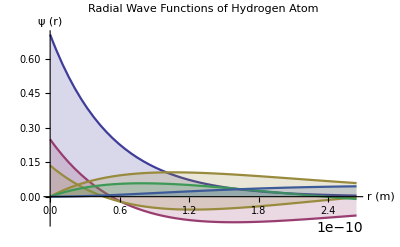

-Graphics-

```mathematica
(*Constants*)
a0=5.29*10^-11 (*Bohr radius in meters*)
E[n_]:=-13.6/n^2 (*Energy eigenvalue function in eV*)
(*Radial wave function for hydrogen atom*)
R[n_,l_,r_]:=Module[{coeff,laguerrePoly},coeff=Sqrt[(Factorial[n-l-1])/(2 n^2 Factorial[n+l])];
laguerrePoly=LaguerreL[n-l-1,2 l,2 r/(n a0)];
coeff (2 r/(n a0))^l Exp[-r/(n a0)] laguerrePoly];

(*Define the range for r*)
rRange={r,0,5*a0}(*5 times the Bohr radius*)
(*Plot the wave functions for n=1,2,3 and l=0,1,2*)waveFunctionPlots=Table[Plot[R[n,l,r],rRange,PlotRange->All,AxesLabel->{"r (m)","ψ (r)"},PlotLabel->StringForm["Radial Wave Function for n = `1`, l = `2`",n,l],Filling->Axis,PlotStyle->ColorData[1][n+l]],{n,1,3},{l,0,Min[n-1,2]}];

(*Plot the energy eigenvalues*)
energyPlots=Plot[E[n],{n,1,3},PlotStyle->{Red,Thick},AxesLabel->{"n","Energy (eV)"},PlotLabel->"Energy Eigenvalues of Hydrogen Atom",Filling->Axis];

(*Show all wave function plots together*)
Show[Evaluate[Flatten[waveFunctionPlots]],PlotLabel->"Radial Wave Functions of Hydrogen Atom",PlotRange->All]

(*Show energy eigenvalue plot*)
energyPlots
```

5.29×10^-11

SetDelayed::write: Tag ⅇ in ⅇ[n_] is Protected.

$Failed

{r,0,2.645×10^-10}

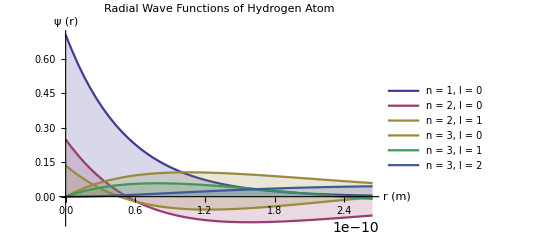

-Graphics-

```mathematica
(*Constants*)
a0=5.29*10^-11(*Bohr radius in meters*)
E[n_]:=-13.6/n^2 (*Energy eigenvalue function in eV*)
(*Radial wave function for hydrogen atom*)
R[n_,l_,r_]:=Module[{coeff,laguerrePoly},coeff=Sqrt[(Factorial[n-l-1])/(2 n^2 Factorial[n+l])];
laguerrePoly=LaguerreL[n-l-1,2 l,2 r/(n a0)];
coeff (2 r/(n a0))^l Exp[-r/(n a0)] laguerrePoly];

(*Define the range for r*)
rRange={r,0,5*a0} (*5 times the Bohr radius*)
(*Plot the wave functions for n=1,2,3 and l=0,1,2*)waveFunctionPlots=Table[Plot[R[n,l,r],rRange,PlotRange->All,AxesLabel->{"r (m)","ψ (r)"},PlotLabel->StringForm["Radial Wave Function for n = `1`, l = `2`",n,l],Filling->Axis,PlotStyle->ColorData[1][Mod[n+l,10]],PlotLegends->Placed[{"n = "<>ToString[n]<>", l = "<>ToString[l]},Below]],{n,1,3},{l,0,Min[n-1,2]}];

(*Plot the energy eigenvalues*)
energyPlots=Plot[E[n],{n,1,3},PlotStyle->{Red,Thick},AxesLabel->{"n","Energy (eV)"},PlotLabel->"Energy Eigenvalues of Hydrogen Atom",Filling->Axis];

(*Show all wave function plots together*)
Show[Evaluate[Flatten[waveFunctionPlots]],PlotLabel->"Radial Wave Functions of Hydrogen Atom",PlotRange->All]

(*Show energy eigenvalue plot*)
energyPlots
```